```mathematica
Nt = 551; (*1000 -> default*)(*10 -> simple case to compare to reduced points*)
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*500 default from problem*)(*200 -> my choice*) (*25 -> simple case to compare to reduced points*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax);

(*For Eigenvalue Plots in Complex Plane*)
(*rs = {0.9,1,1.1};*)
(*rs = {1.4,1.5,1.6};*)(*When exporting RK4 and LD4*)

(*For Max Eigenvalue Plots*)
rs = N[Table[0.01*i,{i,1,30}],32];

PSfinalerrorCN32 = N[Table[0,{i,1,Length[rs]}],32];
PSfinalerrorEuler32 = N[Table[0,{i,1,Length[rs]}],32];
PSfinalerrorRK232 = N[Table[0,{i,1,Length[rs]}],32];
PSfinalerrorRK432 = N[Table[0,{i,1,Length[rs]}],32];
PSfinalerrorLD432 = N[Table[0,{i,1,Length[rs]}],32];

f[x_] =ⅇ^(- 8(x-π)^2);
```

```mathematica
Dimensions[MN]
```

{551,551}

```mathematica
Do[
deltat = N[deltax * rs[[p]],32];


h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];
Xo = N[Xo,32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- 8(x-π)^2);

X = N[X,32];
T = N[T,32];


D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];


(* Crank-Nicolson *)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
(*UCN = Chop[N[UCN,32], 10^(-307)];*)
(*UCN = N[Developer`ToPackedArray[N[UCN,32], Real],32]; 
N[Developer`PackedArrayQ[UCN],32]*)


I1 = N[IdentityMatrix[Length[D1]],32];
I1 = N[I1,32];
A = N[I1 - ((DL / 2)),32];
A = N[A,32];
B = N[I1 + ((DL / 2)),32];
B = N[B,32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = N[EMCN,32];

Do[UCN[[n+1,All]] = N[UCN[[n,All]] + (EMCN ).UCN[[n,All]],32], {n,1,Nt - 1 }];
UCN = N[UCN,32];

FCN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FCN = N[FCN,32];
intCN = N[Table[0,{i,1,Length[FCN[[All,1]]]}],32];
intCN = N[intCN,32];
Do[
FCN[[i]] = N[(D1.UCN[[i,All]])^2,32];

intCN[[i]] = N[(2π)/Nx Total[FCN[[i,All]]],32]
,{i,1,Length[FCN[[All,1]]]}];
intCN = N[intCN,32];

PSfinalerrorCN32[[p]] = N[Abs[Last[intCN] - intCN[[1]]],32]; 



(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = N[URK2,32];
(*URK2 = Chop[N[URK2,32], 10^(-307)];*)
(*URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]*)

IRK2 = N[IdentityMatrix[Length[DL]],32];
IRK2 = N[IRK2,32];

MRK2 = N[(IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2]))),32];
MRK2 = N[MRK2,32];

EMRK2 = N[MRK2 - IRK2,32];
EMRK2 = N[EMRK2,32];

Do[URK2[[n+1,All]] = N[URK2[[n,All]] + (EMRK2).URK2[[n,All]],32], {n,1,Nt - 1 }];
URK2 = N[URK2,32];

FRK2= N[Table[0,{i,1,Nt},{j,1,Nx}]32];
FRK2 = N[FRK2,32];
intRK2 = N[Table[0,{i,1,Length[FRK2[[All,1]]]}],32];
intRK2 = N[intRK2,32];
Do[
FRK2[[i]] = N[(D1.URK2[[i,All]])^2,32];

intRK2[[i]] = N[(2π)/Nx Total[FRK2[[i,All]]],32]
,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = N[intRK2,32];

PSfinalerrorRK232[[p]] = N[Abs[Last[intRK2] - intRK2[[1]]],32];

(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = N[URK4,32];
(*URK4 = Chop[N[URK4,32], 10^(-307)];*)
(*URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]*)

IRK4 = N[IdentityMatrix[Length[DL]],32];
IRK4 = N[IRK4,32];

MRK4 = N[IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])),32];
MRK4 = N[MRK4,32];

EMRK4 = N[MRK4 - IRK4,32];
EMRK4 = N[EMRK4,32];

Do[URK4[[n+1,All]] = N[URK4[[n,All]] + (EMRK4).URK4[[n,All]],32], {n,1,Nt - 1 }];
URK4 = N[URK4,32];

FRK4= N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FRK4 = N[FRK4,32];
intRK4 = N[Table[0,{i,1,Length[FRK4[[All,1]]]}],32];
intRK4 = N[intRK4,32];
Do[
FRK4[[i]] = N[(D1.URK4[[i,All]])^2,32];

intRK4[[i]] = N[(2π)/Nx Total[FRK4[[i,All]]],32]
,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = N[intRK4,32];

PSfinalerrorRK432[[p]] = N[Abs[Last[intRK4] - intRK4[[1]]],32];

(*LD4*)
UN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UN[[1,All]] = N[f[X],32];
UN = N[UN,32];
(*UN = Chop[N[UN,32], 10^(-307)];*)
(*UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]*)


IN = N[IdentityMatrix[Length[D1]],32];
IN = N[IN,32];
AN = N[IN - ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
AN = N[AN,32];
BN = N[IN + ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
BN = N[BN,32];
MN = N[Inverse[AN].BN,32];
MN = N[MN,32];
EMN = N[MN - IN,32];
EMN = N[EMN,32];

Do[UN[[n+1,All]] = N[UN[[n,All]] + (EMN).UN[[n,All]],32], {n,1,Nt - 1 }];
UN = N[UN,32];

FN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FN = N[FN,32];
intN = N[Table[0,{i,1,Length[FN[[All,1]]]}],32];
intN = N[intN,32];
Do[
FN[[i]] = N[(D1.UN[[i,All]])^2,32];

intN[[i]] = N[(2π)/Nx Total[FN[[i,All]]],32]
,{i,1,Length[FN[[All,1]]]}];
intN = N[intN,32];

PSfinalerrorLD432[[p]] = N[Abs[Last[intN] - intN[[1]]],32];


(*For Eigenvalue Plots in Complex Plane*)
(*exportData=Flatten/@Transpose[{realEvalsLD4, imagEvalsLD4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_circle_LD4_"<>ToString[rs[[p]]]<>".dat",exportData,"Table"];*)



,{p,1,Length[rs]}]

(*maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];*)

(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

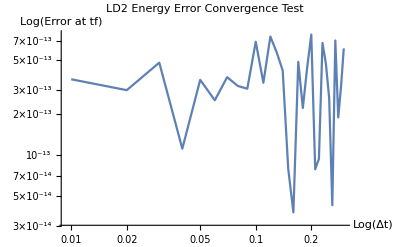

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorCN32}], Joined->True,PlotLabel->"Pseudospectral LD2 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

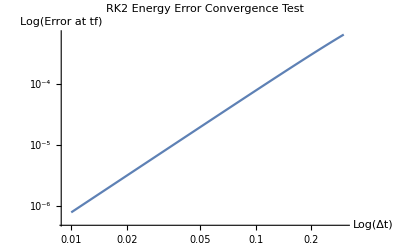

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorRK232}], Joined->True,PlotLabel->"Pseudospectral RK2 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

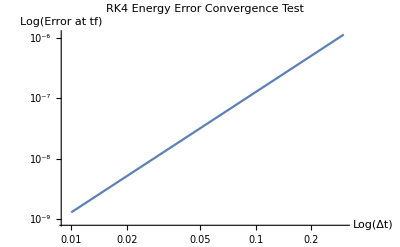

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorRK432}], Joined->True,PlotLabel->"Pseudospectral RK4 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

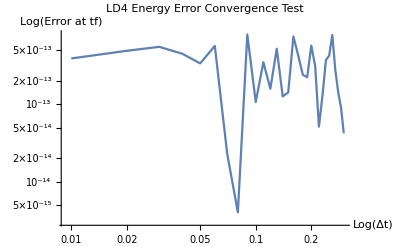

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorLD432}], Joined->True,PlotLabel->"Pseudospectral LD4 Energy Error Convergence Test 32 Digits", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```